# Determinación T_c α=0.5

```mathematica
f[x_,a_,b_,c_,d_] :=a*x^3+b*x^2+c*x+d
```

## L=032

```mathematica
a32 := -652.992117504792
b32 := 3304.77816266688
c32 :=-5576.11585556628
d32 := 3137.35224589408

a32err := 1440.53498315635
b32err := 7350.66060946822
c32err := 12502.7477550555
d32err := 7088.61032972504
```

## L=064

```mathematica
a64 := 877.343443175282
b64 := -4543.1075081726
c64 := 7837.3396806785
d64 := -4503.66926342001

a64err := 1553.2542263257
b64err := 7925.83642039402
c64err := 13481.0649780762
d64err := 7643.28115190621
```

## L=128

```mathematica
a128 := -2845.60928029868
b128 := 14285.4913463527
c128 := -23904.1845972957
d128:= 13333.1426621889

a128err := 1314.18734077567
b128err := 6702.15973736977
c128err := 11393.264423961
d128err := 6455.91029810856
```

## L=256

```mathematica
a256 := -26516.3907305505
b256 := 134449.453897246
c256 := -227239.419507953
d256:= 128023.747419179

a256err := 1667.57175095347
b256err := 8505.23102007552
c256err := 14459.8239900965
d256err := 8194.36306958942
```

## L=512

```mathematica
a512 := 36307.3353886447
b512 :=-188006.047184362
c512 :=324418.681921305
d512 := -186551.575906199

a512err := 41928.2806984627
b512err := 214122.474617365
c512err := 364497.222724316
d512err := 206824.967092101
```

#### Entre L=128 y L=064

{{x→1.67783-0.0142173 ⅈ},{x→1.67783+0.0142173 ⅈ},{x→1.70179}}

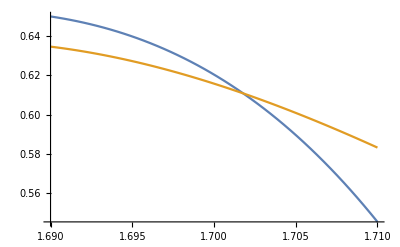

```mathematica
Solve[f[x,a128,b128,c128,d128]==f[x,a64,b64,c64,d64],x]
Plot[{f[x,a128,b128,c128,d128],f[x,a64,b64,c64,d64]},{x,1.69,1.71}]
```

#### Entre L=064 y L=032

{{x→1.6803},{x→1.70137},{x→1.74654}}

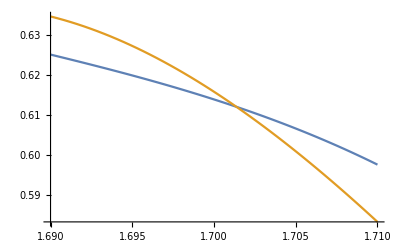

```mathematica
Solve[f[x,a64,b64,c64,d64]==f[x,a32,b32,c32,d32],x]
Plot[{f[x,a32,b32,c32,d32],f[x,a64,b64,c64,d64]},{x,1.69,1.71}]
```

## Entre L=256 y L=128

{{x→1.68735-0.00546249 ⅈ},{x→1.68735+0.00546249 ⅈ},{x→1.70176}}

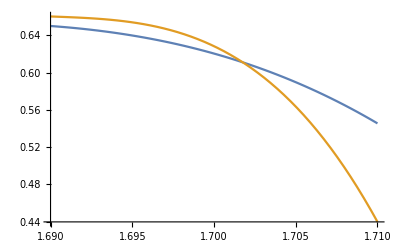

```mathematica
Solve[f[x,a128,b128,c128,d128]==f[x,a256,b256,c256,d256],x]
Plot[{f[x,a128,b128,c128,d128],f[x,a256,b256,c256,d256]},{x,1.69,1.71}]
```

## Entre L=512 y L=256

{{x→1.69484},{x→1.70148},{x→1.73639}}

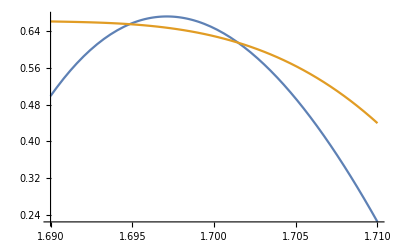

```mathematica
Solve[f[x,a512,b512,c512,d512]==f[x,a256,b256,c256,d256],x]
Plot[{f[x,a512,b512,c512,d512],f[x,a256,b256,c256,d256]},{x,1.69,1.71}]
```